## №1

```mathematica
n=2;
```

```mathematica
m=3;
```

```mathematica
SS=Table[Subscript[S, i]=i,{i,0,m}]
```

{0,1,2,3}

```mathematica
μ=((n+m)!)/(n!m!)
```

10

```mathematica
t={};
```

```mathematica
i=1;
```

```mathematica
Do[If[j+k<m+1,{t=Join[t,{{Subscript[S, j],Subscript[S, k]}}],Subscript[ϕ, i][x_,y_]=x^Subscript[S, j] y^Subscript[S, k],i=i+1}],{j,0,m},{k,0,m}]
```

```mathematica
t
```

{{0,0},{0,1},{0,2},{0,3},{1,0},{1,1},{1,2},{2,0},{2,1},{3,0}}

```mathematica
i
```

11

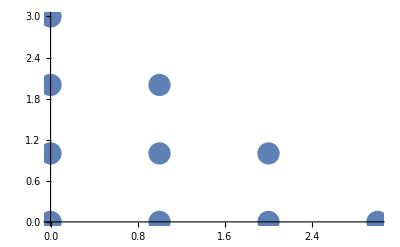

```mathematica
ListPlot[t,PlotStyle->PointSize[0.04]]
```

```mathematica
Table[Subscript[ϕ, i][x,y],{i,1,μ}]
```

{1,y,y^2,y^3,x,x y,x y^2,x^2,x^2 y,x^3}

## №2

```mathematica
V=Table[Subscript[ϕ, j][t[[i,1]],t[[i,2]]],{i,1,μ},{j,1,μ}]
```

{{1,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0},{1,2,4,8,0,0,0,0,0,0},{1,3,9,27,0,0,0,0,0,0},{1,0,0,0,1,0,0,1,0,1},{1,1,1,1,1,1,1,1,1,1},{1,2,4,8,1,2,4,1,2,1},{1,0,0,0,2,0,0,4,0,8},{1,1,1,1,2,2,2,4,4,8},{1,0,0,0,3,0,0,9,0,27}}

```mathematica
Det[V]≠0
```

True

## №3

```mathematica
f[x_,y_]=x*Sin[x + y];
```

```mathematica
eqv:=Table[∑_(i=1)^μ (Subscript[b, i]*Subscript[ϕ, i][t[[j,1]],t[[j,2]]])==f[t[[j,1]],t[[j,2]]],{j,1,μ}]
```

```mathematica
koef:=Solve[eqv,{}]//Flatten
koef
```

{b_1→0,b_2→0,b_3→0,b_4→0,b_5→3 Sin[1]-3 Sin[2]+Sin[3],b_6→1/2 (-5 Sin[1]+8 Sin[2]-3 Sin[3]),b_7→1/2 (Sin[1]-2 Sin[2]+Sin[3]),b_8→1/2 (-5 Sin[1]+8 Sin[2]-3 Sin[3]),b_9→Sin[1]-2 Sin[2]+Sin[3],b_10→1/2 (Sin[1]-2 Sin[2]+Sin[3])}

```mathematica
P[x_,y_]:=∑_(i=1)^μ Subscript[b, i] Subscript[ϕ, i][x,y]//.koef
```

```mathematica
P[x,y]
```

1/2 x^2 (-5 Sin[1]+8 Sin[2]-3 Sin[3])+1/2 x y (-5 Sin[1]+8 Sin[2]-3 Sin[3])+x (3 Sin[1]-3 Sin[2]+Sin[3])+1/2 x^3 (Sin[1]-2 Sin[2]+Sin[3])+x^2 y (Sin[1]-2 Sin[2]+Sin[3])+1/2 x y^2 (Sin[1]-2 Sin[2]+Sin[3])

```mathematica
Table[P[t[[j,1]],t[[j,2]]]==f[t[[j,1]],t[[j,2]]],{j,1,μ}]
```

{True,True,True,True,True,True,True,True,True,True}

## №5

```mathematica
ListPlot[t,PlotStyle->PointSize[0.04]]
```

-Graphics-

```mathematica
Gr1=Plot3D[f[x,y],{x,0,m},{y,0,m}]
```

-Graphics3D-

```mathematica
Gr2=Plot3D[P[x,y],{x,0,m},{y,0,m}]
```

-Graphics3D-

```mathematica
Tb1=Table[Point[{t[[j,1]],t[[j,2]],f[t[[j,1]],t[[j,2]]]}],{j,1,μ}];
```

```mathematica
Gr3=Graphics3D[{AbsolutePointSize[5],Tb1}];
```

```mathematica
Show[Gr1,Gr2,Gr3]
```

-Graphics3D-

```mathematica
Table[{f[x_,y_]=Subscript[ϕ, i][x,y],P[x,y]==Subscript[ϕ, i][x,y]},{i,1,μ}]
```

{{1,True},{y,True},{y^2,True},{y^3,True},{x,True},{x y,True},{x y^2,True},{x^2,True},{x^2 y,True},{x^3,True}}